# Parallelized ICS Interaction Optimisation + Tuning Curves

## Units, Constants, Cases + Optimisation Parameters

```mathematica
(*Units*)
```

```mathematica
MeV=10^6;
nm=10^-9;
mm=10^-3;
mrad=10^-3;
μrad=10^-6;
nrad=10^-9;
μm=10^-6;
pC=10^-12;
nC=10^-9;
μJ=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
```

```mathematica
me=0.51099895MeV;
h=4.135667696*10^-15; (*in eV*)
clight=299792458;
echarge=1.60217662*10^-19;
σT=6.6524587158*10^-29;
fivedeg=(5*π)/180;
```

```mathematica
(*Cases*)
```

```mathematica
CBETA150 = {Ee->150MeV,λ->1064nm,ϵn->0.3mm mrad,ϕ->fivedeg,σL->25μm,Q->32pC,Epulse->62μJ,f->162.5MHz,tpulse->10ps,σze->1mm,ΔEe->5*10^-4,Δλ->6.57*10^-4};

DIANA340={Ee->340MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA680={Ee->680MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1020={Ee->1020MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

MAXIIIeq={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->17.5471mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinj={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
```

```mathematica
trialcase=CBETA150;
```

## Intermediaries

```mathematica
γ[Ee_]:=(Ee+me)/me;
EL[λ_]:=(h*clight)/λ;
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Bandwidth Terms

```mathematica
collterm[Ee_,λ_,θ_]:=1/Sqrt[12]*ψ[Ee,θ]^2/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θ_]:=(2+Xrec[Ee,λ])/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θ_]:=(1+ψ[Ee,θ]^2)/(1+Xrec[Ee,λ]+ψ[Ee,θ]^2)*Δλ;
```

## Flux Intermediaries

```mathematica
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

## β^* Calculation

```mathematica
βstar[Ee_,ϵn_,BW_,λ_,ΔEe_,Δλ_,θ_]:=(2*γ[Ee]*ϵn)/Sqrt[BW^2-(collterm[Ee,λ,θ]^2+beamspreadterm[Ee,λ,ΔEe,θ]^2+laserspreadterm[Ee,λ,Δλ,θ]^2)];
```

## Uncollimated Flux Calculation

```mathematica
F[Ee_,λ_,Q_,Epulse_,f_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_]:=σc[Ee,λ]*(Ne[Q]*NL[Epulse,λ]*f*Cos[ϕ/2])/(2*π*convxy[βIP,ϵn,Ee,σL]*Sqrt[convxy[βIP,ϵn,Ee,σL]^2*Cos[ϕ/2]^2+convz[σze,tpulse]^2*Sin[ϕ/2]^2]);
```

## Collimated Flux Calculation

```mathematica
Fψ[Ee_,λ_,Q_,Epulse_,f_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,θ_]:=Sqrt[2]/π*F[Ee,λ,Q,Epulse,f,ϕ,βIP,ϵn,σL,σze,tpulse]*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θ]^2)/3)*ψ[Ee,θ]^2)/((1+(1+Xrec[Ee,λ]/2)*ψ[Ee,θ]^2)*(1+ψ[Ee,θ]^2));
```

# Single Fixed Bandwidth Optimisation

```mathematica
(*Optimisation Parameters*)
BW=0.5/100;
θmax=5mrad;
θstep=100nrad;(*μrad typically used for tuning curves, 10 nrad used for single cases*)
```

## β^*-θ_col Pairings

```mathematica
βstardat=Table[{θ,Re[βstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ]]/.trialcase},{θ,0,θmax,θstep}]//AbsoluteTiming;
simtime={βstardat⟦1⟧};
```

```mathematica
imaginarycut=Min[Position[βstardat⟦2⟧⟦All,2⟧,0.]]//AbsoluteTiming;
AppendTo[simtime,imaginarycut⟦1⟧];
```

```mathematica
βstardat=βstardat⟦2⟧⟦1;;(imaginarycut⟦2⟧-1),All⟧//AbsoluteTiming;
AppendTo[simtime,βstardat⟦1⟧];
```

β^*is calculated for each step in the range 0 to θmax. The position at which β^* becomes imaginary is found and then the imaginary values are discarded.

## Collimated Flux Maximisation

```mathematica
Fψdat=Table[{βstardat⟦2⟧⟦i,1⟧,βstardat⟦2⟧⟦i,2⟧,Fψ[Ee,λ,Q,Epulse,f,ϕ,βstardat⟦2⟧⟦i,2⟧,ϵn,σL,σze,tpulse,βstardat⟦2⟧⟦i,1⟧]/.trialcase},{i,1,(imaginarycut⟦2⟧-1),1}]//AbsoluteTiming;
AppendTo[simtime,Fψdat⟦1⟧];
```

```mathematica
maxval=Position[Fψdat⟦2⟧⟦All,3⟧,Max[Fψdat⟦2⟧⟦All,3⟧]]⟦1,1⟧;
```

```mathematica
(Fψdat⟦2⟧⟦maxval,1⟧)/mrad//N
Fψdat⟦2⟧⟦maxval,2⟧
Fψdat⟦2⟧⟦maxval,3⟧
```

0.4333

0.125998

2.09394×10^8

```mathematica
Total[simtime]
```

14.7171

# Tuning Curve Optimisation

```mathematica
(*Optimisation Parameters*)
BWmin=Sqrt[(2*ΔEe/.trialcase)^2+(Δλ/.trialcase)^2]; 
BWmax=1/100;
BWstep=10^-3/100;
θmax=5mrad;
θstep=μrad;(*μrad typically used for tuning curves, 10 nrad used for single cases*)
```

## β^*-θ_col Pairings

Nested computations like nested tables can’t both be parallelized. Therefore, only the inner table (the more computationally intensive) is parallelized.

```mathematica
LaunchKernels[15];
```

```mathematica
DistributeDefinitions[βstar,BWmin,BWmax,BWstep,θmax,θstep,Fψ];
```

```mathematica
βstardatcurve=Table[{BW,ParallelTable[{θ,Re[βstar[Ee,ϵn,BW,λ,ΔEe,Δλ,θ]]/.trialcase},{θ,0,θmax,θstep}]},{BW,BWmin,BWmax,BWstep}]//AbsoluteTiming;
```

```mathematica
simtime={βstardatcurve⟦1⟧};
```

```mathematica
CloseKernels[];
```

```mathematica
imaginarycuts=Table[Min[Position[βstardatcurve⟦2⟧⟦i,2⟧⟦All,2⟧,0.]],{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,imaginarycuts⟦1⟧];
```

```mathematica
βstardatcurve=Table[{βstardatcurve⟦2⟧⟦i,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦1;;(imaginarycuts⟦2⟧⟦i⟧-1),All⟧},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,βstardatcurve⟦1⟧];
```

## Collimated Flux Maximisation

```mathematica
LaunchKernels[15];
```

```mathematica
DistributeDefinitions[Fψ,βstardatcurve,imaginarycuts];
```

```mathematica
Fψdatcurve=Table[{βstardatcurve⟦2⟧⟦i,1⟧,ParallelTable[{βstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧,βstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,Fψ[Ee,λ,Q,Epulse,f,ϕ,βstardatcurve⟦2⟧⟦i,2⟧⟦j,2⟧,ϵn,σL,σze,tpulse,βstardatcurve⟦2⟧⟦i,2⟧⟦j,1⟧]/.trialcase},{j,1,(imaginarycuts⟦2⟧⟦i⟧-1)}]},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
```

```mathematica
AppendTo[simtime,Fψdatcurve⟦1⟧];
```

```mathematica
CloseKernels[];
```

```mathematica
maxvals=Table[Position[Fψdatcurve⟦2⟧⟦i,2⟧⟦All,3⟧,Max[Fψdatcurve⟦2⟧⟦i,2⟧⟦All,3⟧]]⟦1,1⟧,{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,maxvals⟦1⟧];
```

```mathematica
maxdata=Table[{Fψdatcurve⟦2⟧⟦i,1⟧*100,(Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,1⟧)/mrad,Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,2⟧,Fψdatcurve⟦2⟧⟦All,2⟧⟦i,maxvals⟦2⟧⟦i⟧,3⟧},{i,1,((BWmax-BWmin)/BWstep)}]//AbsoluteTiming;
AppendTo[simtime,maxdata⟦1⟧];
```

The maxdata array is of the form BW, θcol, β^*, F_ψ . All of the necessary data is available in this singular array.

```mathematica
Total[simtime]
```

616.316

```mathematica
simtime
```

{279.219,3.30221,1.50062,331.679,0.313815,0.301272}

## Saving Data

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat"];
maxdata⟦2⟧>>"DIANA1020opt.txt";
```

## Plotting Data

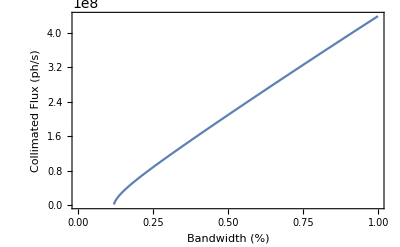

```mathematica
ListLinePlot[Partition[Riffle[maxdata⟦2⟧⟦All,1⟧,maxdata⟦2⟧⟦All,4⟧],2],Frame->True,FrameLabel->{"Bandwidth (%)","Collimated Flux (ph/s)"},LabelStyle->16]
```

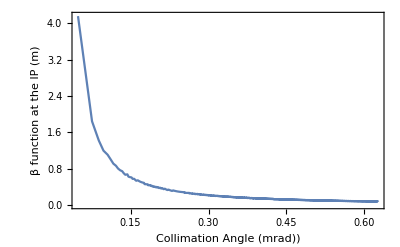

```mathematica
ListLinePlot[Partition[Riffle[maxdata⟦2⟧⟦All,2⟧,maxdata⟦2⟧⟦All,3⟧],2],Frame->True,FrameLabel->{"Collimation Angle (mrad))","β function at the IP (m)"},LabelStyle->16,PlotRange->Full]
```

# Benchmarking

```mathematica
KernelvsTime={{1,5,10,15,20,25,30},{1529.30,681.59,631.78,599.68,605.57,602.04,616.32}/60};
```

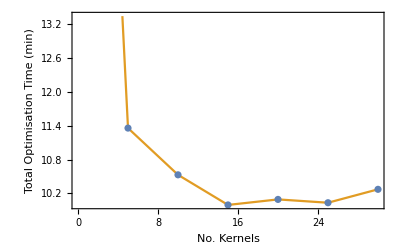

```mathematica
ListPlot[{Transpose[KernelvsTime],Transpose[KernelvsTime]},Joined->{False,True},Frame->True,LabelStyle->15,FrameLabel->{"No. Kernels","Total Optimisation Time (min)"}]
```

# Multiple Case Plotting

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/TuningDat"];
optMAXIIIinj=<<"MAXIIIinjopt.txt";
optMAXIIIeq=<<"MAXIIIeqopt.txt";

optDIANA340=<<"DIANA340opt.txt";
optDIANA680=<<"DIANA680opt.txt";
optDIANA1020=<<"DIANA1020opt.txt";
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## MAXIII Non-Eq ICS Plots

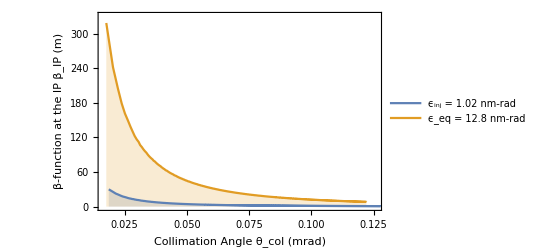

```mathematica
ListLinePlot[{Partition[Riffle[optMAXIIIinj⟦All,2⟧,optMAXIIIinj⟦All,3⟧],2],Partition[Riffle[optMAXIIIeq⟦All,2⟧,optMAXIIIeq⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"ϵ_inj = 1.02 nm-rad","ϵ_eq = 12.8 nm-rad"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->{{0.0165,0.126},{0,330}},Filling->Axis]
```

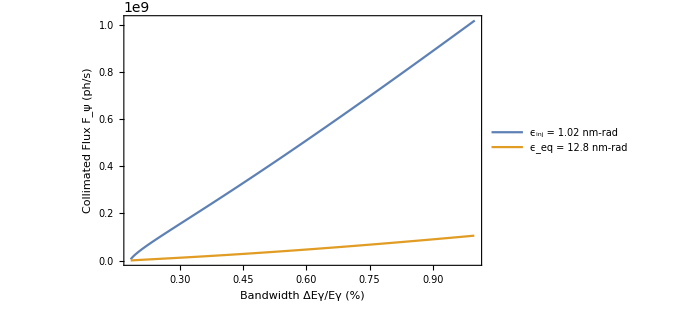

```mathematica
ListLinePlot[{Partition[Riffle[optMAXIIIinj⟦All,1⟧,optMAXIIIinj⟦All,4⟧],2],Partition[Riffle[optMAXIIIeq⟦All,1⟧,optMAXIIIeq⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔEγ/Eγ (%)","Collimated Flux F_ψ (ph/s)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"ϵ_inj = 1.02 nm-rad","ϵ_eq = 12.8 nm-rad"},LabelStyle->12,LegendFunction->frame],{0.2,0.7}],PlotRange->Full]
```

## DIANA Plots

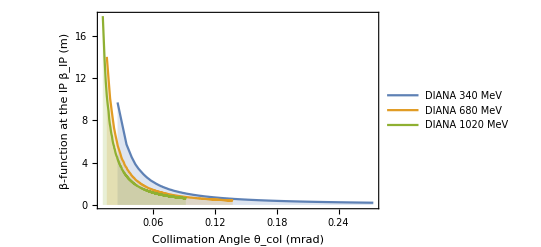

```mathematica
ListLinePlot[{Partition[Riffle[optDIANA340⟦All,2⟧,optDIANA340⟦All,3⟧],2],Partition[Riffle[optDIANA680⟦All,2⟧,optDIANA680⟦All,3⟧],2],Partition[Riffle[optDIANA1020⟦All,2⟧,optDIANA1020⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"DIANA 340 MeV","DIANA 680 MeV","DIANA 1020 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->Full,Filling->Axis]
```

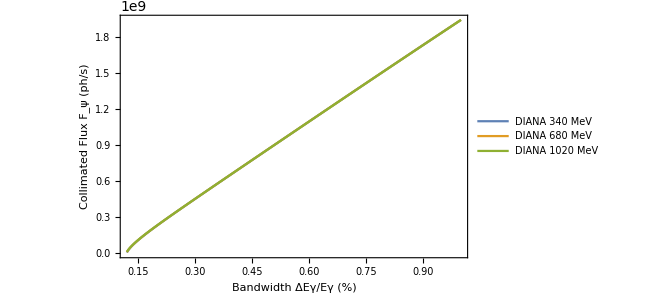

```mathematica
ListLinePlot[{Partition[Riffle[optDIANA340⟦All,1⟧,optDIANA340⟦All,4⟧],2],Partition[Riffle[optDIANA680⟦All,1⟧,optDIANA680⟦All,4⟧],2],Partition[Riffle[optDIANA1020⟦All,1⟧,optDIANA1020⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔEγ/Eγ (%)","Collimated Flux F_ψ (ph/s)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"DIANA 340 MeV","DIANA 680 MeV","DIANA 1020 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.25}],PlotRange->Full]
```

## DIANA vs MAXIII Non-Eq Ring Plots

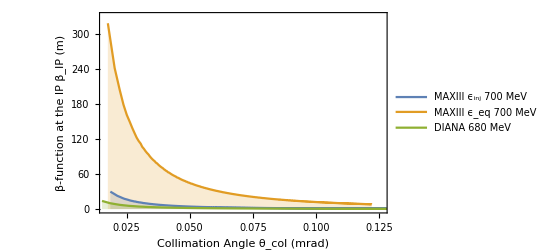

```mathematica
ListLinePlot[{Partition[Riffle[optMAXIIIinj⟦All,2⟧,optMAXIIIinj⟦All,3⟧],2],Partition[Riffle[optMAXIIIeq⟦All,2⟧,optMAXIIIeq⟦All,3⟧],2],Partition[Riffle[optDIANA680⟦All,2⟧,optDIANA680⟦All,3⟧],2]},Frame->True,FrameLabel->{"Collimation Angle θ_col (mrad)","β-function at the IP β_IP (m)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"MAXIII ϵ_inj 700 MeV","MAXIII ϵ_eq 700 MeV", "DIANA 680 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}],PlotRange->{{0.0165,0.126},{0,330}},Filling->Axis]
```

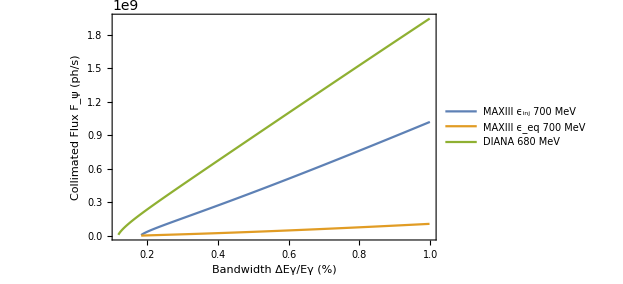

```mathematica
ListLinePlot[{Partition[Riffle[optMAXIIIinj⟦All,1⟧,optMAXIIIinj⟦All,4⟧],2],Partition[Riffle[optMAXIIIeq⟦All,1⟧,optMAXIIIeq⟦All,4⟧],2],Partition[Riffle[optDIANA680⟦All,1⟧,optDIANA680⟦All,4⟧],2]},Frame->True,FrameLabel->{"Bandwidth ΔEγ/Eγ (%)","Collimated Flux F_ψ (ph/s)"},LabelStyle->16,PlotLegends->Placed[LineLegend[{"MAXIII ϵ_inj 700 MeV","MAXIII ϵ_eq 700 MeV","DIANA 680 MeV"},LabelStyle->12,LegendFunction->frame],{0.25,0.7}],PlotRange->Full]
```